```mathematica
ClearAll["Global`*"]
```

```mathematica
f1[n_,c_] := f1[n,c]=( Sum[ 1, {j,1,Floor[c^2 n]},{k,1,Floor[c^2 n / j ]}] - 2 Sum[ 1, {j,1,Floor[c]},{k,1,Floor[c^2 n / j]}] + Sum[ 1, {j,1,Floor[c]},{k,1,Floor[c]}])/c^2
```

```mathematica
N[f1[4,1]]
```

1.

```mathematica
N[Gamma[2,0,-Log[4]]/Gamma[2]]
```

2.54518-6.23389×10^-16 ⅈ

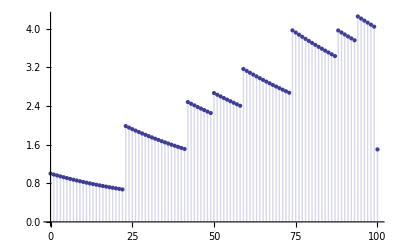

```mathematica
DiscretePlot[ f1[4,1+c*.01],{c,0,100}]
```

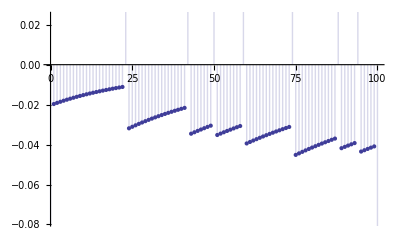

```mathematica
DiscretePlot[ f1[4,1+c*.01]-f1[4,1+(c-1)*.01],{c,0,100}]
```

```mathematica
f2[c_] := f1[100,c]
```

```mathematica
f2[1]
```

283